```mathematica
fittest = ProportionateRankedSelection[population,10];
```

```mathematica
childrenPerCouple = (2 Length[population])/10
```

10

```mathematica
g1 = First@fittest[[All,"Genome"]][[1]]; l1 = Last@fittest[[All,"Genome"]][[1]];
g2 = First@fittest[[All,"Genome"]][[2]];l2 =Last@fittest[[All,"Genome"]][[2]];
```

```mathematica
l1
```

{1→Func[TimesFunc],2→Term[2],3→Term[x]}

```mathematica
l2
```

{1→Func[TimesFunc],2→Term[y],3→Term[1]}

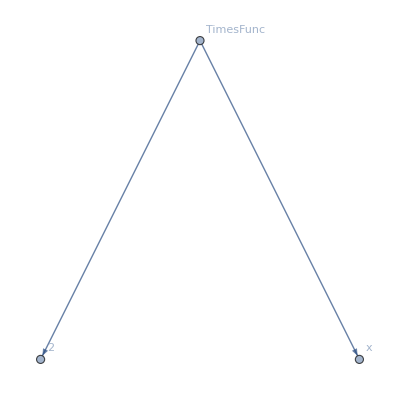
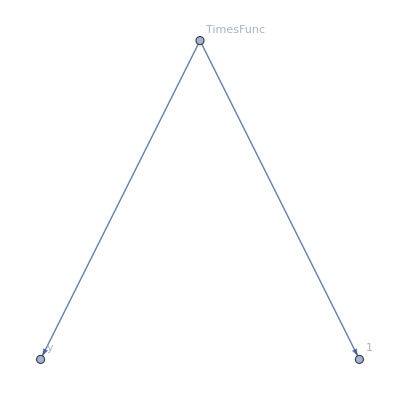

```mathematica
{g1,g2}
```

```mathematica
vertex1 = 3;
vertex2 = 1;
```

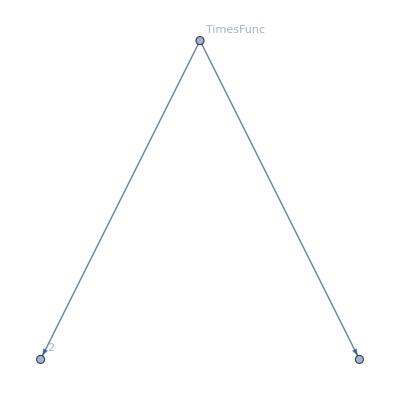
{-Graphics-,{1→Func[TimesFunc],2→Term[2]}}

```mathematica
cropped = DeleteSubtree[g1,l1,vertex1]
```

```mathematica
sub = Subtree[g2,l2,vertex2]
```

{-Graphics-,{1→Func[TimesFunc],2→Term[y],3→Term[1]}}

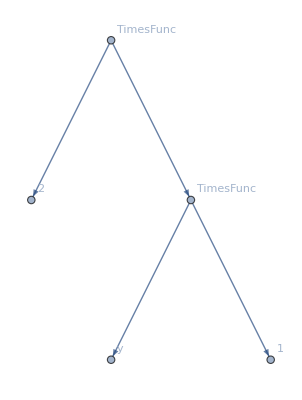
{-Graphics-,{1→Func[TimesFunc],2→Term[2],3→Func[TimesFunc],4→Term[y],5→Term[1]}}

```mathematica
InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
```

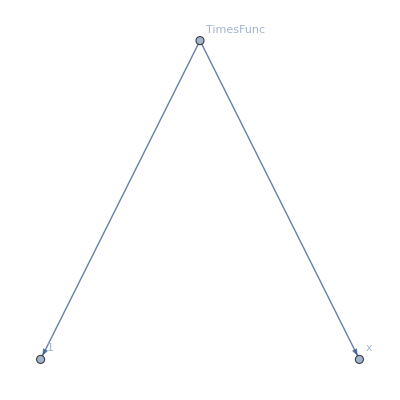
{-Graphics-,{1→Func[TimesFunc],2→Term[1],3→Term[x]}}

```mathematica
Crossover[g1,l1,g2,l2]
```

## Tree insertion

```mathematica
edges = DeleteCases[VertexList[First[cropped]],Empty]
```

{1,2}

```mathematica
missing = Complement[Range[Max[edges]],edges]
```

{}

```mathematica
missingRules = Thread[Take[VertexList[First[sub]],UpTo[Length[missing]]]->Take[missing,UpTo[Length[VertexList[First[sub]]]]]]
```

{}

```mathematica
Length[VertexList[First[sub]]]-Length[missing]
```

3

```mathematica
newRules = Thread[Drop[VertexList[First[sub]],Length[missing]]-> Range[Max[edges]+1,Max[edges]+Length[VertexList[First[sub]]]-Length[missing]]]
```

{1→3,2→4,3→5}

```mathematica
insertionRules = Join[missingRules,newRules]
```

{1→3,2→4,3→5}

```mathematica
EdgeList[First[sub]]
```

{1->2,1->3}

```mathematica
Last[sub]
```

{1→Func[TimesFunc],2→Term[y],3→Term[1]}

```mathematica
EvaluateFunction[PowerFunc[x,0],{{0,0,1},{0,1,2},{0,2,9},{0,3,28},{0,4,65},{0,5,126},{0,6,217},{0,7,344},{0,8,513},{0,9,730},{0,10,1001},{1,0,4},{1,1,5},{1,2,12},{1,3,31},{1,4,68},{1,5,129},{1,6,220},{1,7,347},{1,8,516},{1,9,733},{1,10,1004},{2,0,21},{2,1,22},{2,2,29},{2,3,48},{2,4,85},{2,5,146},{2,6,237},{2,7,364},{2,8,533},{2,9,750},{2,10,1021},{3,0,88},{3,1,89},{3,2,96},{3,3,115},{3,4,152},{3,5,213},{3,6,304},{3,7,431},{3,8,600},{3,9,817},{3,10,1088},{4,0,265},{4,1,266},{4,2,273},{4,3,292},{4,4,329},{4,5,390},{4,6,481},{4,7,608},{4,8,777},{4,9,994},{4,10,1265},{5,0,636},{5,1,637},{5,2,644},{5,3,663},{5,4,700},{5,5,761},{5,6,852},{5,7,979},{5,8,1148},{5,9,1365},{5,10,1636},{6,0,1309},{6,1,1310},{6,2,1317},{6,3,1336},{6,4,1373},{6,5,1434},{6,6,1525},{6,7,1652},{6,8,1821},{6,9,2038},{6,10,2309},{7,0,2416},{7,1,2417},{7,2,2424},{7,3,2443},{7,4,2480},{7,5,2541},{7,6,2632},{7,7,2759},{7,8,2928},{7,9,3145},{7,10,3416},{8,0,4113},{8,1,4114},{8,2,4121},{8,3,4140},{8,4,4177},{8,5,4238},{8,6,4329},{8,7,4456},{8,8,4625},{8,9,4842},{8,10,5113},{9,0,6580},{9,1,6581},{9,2,6588},{9,3,6607},{9,4,6644},{9,5,6705},{9,6,6796},{9,7,6923},{9,8,7092},{9,9,7309},{9,10,7580},{10,0,10021},{10,1,10022},{10,2,10029},{10,3,10048},{10,4,10085},{10,5,10146},{10,6,10237},{10,7,10364},{10,8,10533},{10,9,10750},{10,10,11021}},True]
```

0.

```mathematica
expr = PowerFunc[x,0];
testInput = Map[Thread[{x,y}->#]&,pts[[All,1;;2]]];
```

```mathematica
testFunctions = Map[expr/.#&,testInput];
```

```mathematica
testResults =Quiet[testFunctions/.{PlusFunc->Plus,TimesFunc->Times,PowerFunc->Power}];
```

```mathematica
error = Mean[Abs[testResults-pts[[All,3]]]];
```

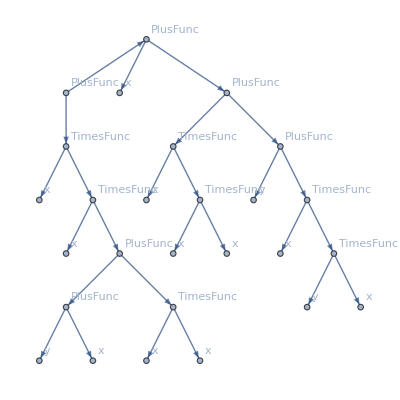
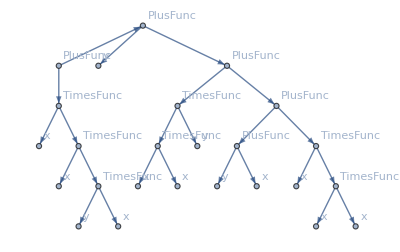
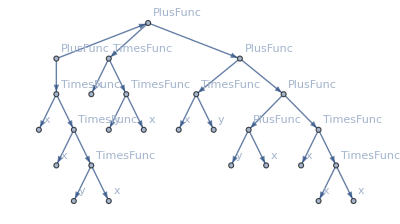
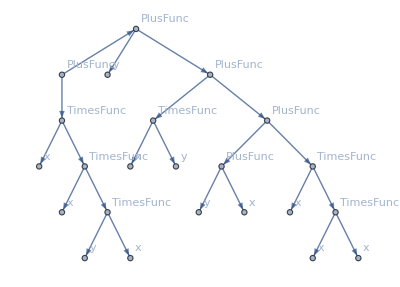
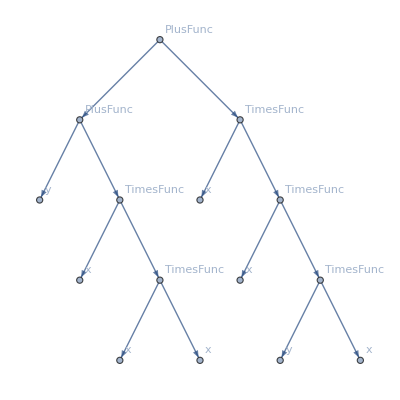
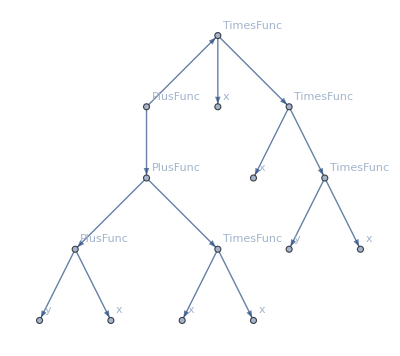
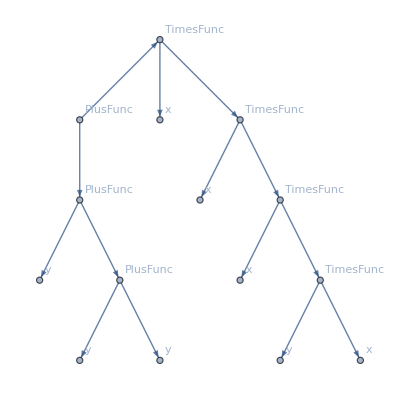
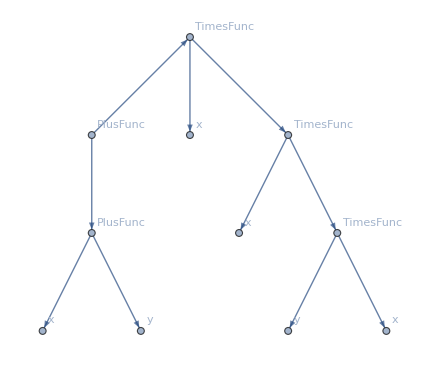
{<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Func[PlusFunc],11→Func[TimesFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[4],15→Func[TimesFunc],16→Term[y],17→Func[PlusFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Term[x],25→Term[x],26→Term[y],27→Term[x]}},Score→0.00180825|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Func[TimesFunc],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Term[x]}},Score→0.00105507|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[TimesFunc],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[y],27→Term[x]}},Score→0.00105166|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.00103546|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.00102285|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PlusFunc],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Term[x],14→Term[y],15→Term[x]}},Score→0.000852472|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[PlusFunc],4→Term[y],5→Func[PlusFunc],6→Term[3],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[x],11→Func[TimesFunc],12→Term[y],13→Term[y],14→Term[y],15→Term[x]}},Score→0.000834223|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[x],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000829163|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Term[x],3→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000825979|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.000742144|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[4],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x]}},Score→0.000720029|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[TimesFunc],3→Func[TimesFunc],4→Term[x],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[y],15→Term[x]}},Score→0.000683971|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Term[x]}},Score→0.00068354|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Term[x]}},Score→0.00068354|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[TimesFunc],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Term[y],14→Term[x],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x]}},Score→0.00068311|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Func[TimesFunc],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[x],27→Func[TimesFunc],28→Term[y],29→Term[x]}},Score→0.000654531|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000649064|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[y],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000648612|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x]}},Score→0.000595081|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Func[PlusFunc],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Func[PlusFunc],25→Func[TimesFunc],26→Term[x],27→Term[x],28→Term[y],29→Term[x]}},Score→0.000534268|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[y],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x]}},Score→0.000521717|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.000446387|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Term[y]}},Score→0.000415785|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Term[x]}},Score→0.000415785|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Term[x],12→Term[y],13→Term[y]}},Score→0.000393684|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Term[x]}},Score→0.000392917|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Term[y]}},Score→0.000391379|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[y],7→Term[x]}},Score→0.000391379|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[x],4→Term[y],5→Func[PlusFunc],12→Term[y],13→Term[y]}},Score→0.000389092|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[y],4→Term[y],5→Func[PlusFunc],12→Term[y],13→Term[y]}},Score→0.000389089|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Term[y],4→Term[y],5→Term[y]}},Score→0.000388339|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Func[TimesFunc],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Term[x]}},Score→0.000122352|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Func[TimesFunc],12→Term[y],13→Term[y],14→Term[x],15→Term[x]}},Score→0.000105257|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Term[y],11→Func[TimesFunc],12→Term[y],13→Func[TimesFunc],14→Term[x],15→Term[x]}},Score→0.000103465|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Func[TimesFunc],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[x],25→Func[TimesFunc],26→Term[x],27→Term[x]}},Score→0.000010143|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[x],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Func[PlusFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[y],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x],20→Term[x],21→Func[TimesFunc],22→Term[x],23→Term[x]}},Score→6.43102×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Func[PlusFunc],11→Term[x],12→Term[y],13→Term[y],14→Func[TimesFunc],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[x],19→Term[x],20→Term[y],21→Term[x]}},Score→5.2932×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Func[PlusFunc],11→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[y],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x],24→Term[y],25→Func[PlusFunc],26→Func[TimesFunc],27→Func[PlusFunc],28→Term[y],29→Func[TimesFunc],30→Term[x],31→Func[TimesFunc],32→Term[y],33→Term[x],34→Term[x],35→Func[TimesFunc],36→Term[x],37→Term[x]}},Score→3.5611×10^-6|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PowerFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[PlusFunc],13→Func[TimesFunc],14→Term[x],15→Func[TimesFunc],16→Term[x],17→Func[TimesFunc],18→Term[y],19→Term[x],20→Term[y],21→Func[PlusFunc],22→Func[TimesFunc],23→Func[PlusFunc],24→Term[y],25→Func[TimesFunc],26→Term[x],27→Func[TimesFunc],28→Term[2],29→Term[x],30→Term[x],31→Func[TimesFunc],32→Term[x],33→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PowerFunc],3→Func[TimesFunc],4→Term[x],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[PlusFunc],10→Func[PlusFunc],11→Func[TimesFunc],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Func[TimesFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x],22→Term[x],23→Term[x],24→Term[x],25→Term[x],26→Term[y],27→Term[3]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[y],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[x],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[PowerFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[TimesFunc],3→Func[TimesFunc],4→Term[x],5→Func[TimesFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Func[PlusFunc],13→Func[TimesFunc],14→Term[y],15→Term[x],16→Term[y],17→Func[PlusFunc],18→Term[x],19→Func[PowerFunc],20→Term[y],21→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PowerFunc],3→Func[TimesFunc],4→Term[y],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[y],9→Term[x],12→Func[TimesFunc],13→Func[PlusFunc],14→Term[x],15→Term[x],16→Func[PlusFunc],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[x],21→Term[x],22→Term[y],23→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[3],5→Func[PlusFunc],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[x],13→Func[PowerFunc],16→Term[y],17→Func[TimesFunc],18→Term[x],19→Func[TimesFunc],20→Term[y],21→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PowerFunc],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Func[PlusFunc],12→Term[y],13→Func[PlusFunc],14→Term[x],15→Func[PowerFunc],16→Term[y],17→Term[x],18→Term[y],19→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Func[PlusFunc],5→Term[y],6→Term[x],7→Func[TimesFunc],8→Term[x],9→Func[TimesFunc],10→Term[y],11→Term[x],12→Term[y],13→Func[PlusFunc],14→Term[x],15→Func[PowerFunc],16→Term[y],17→Term[x]}},Score→0.|>,<|Genome→{-Graphics-,{1→Func[PlusFunc],2→Func[PlusFunc],3→Func[TimesFunc],4→Term[y],5→Term[y],6→Term[x],7→Func[PlusFunc],8→Term[y],9→Func[PlusFunc],10→Term[x],11→Func[PowerFunc],12→Term[y],13→Term[x]}},Score→0.|>}

```mathematica
Reverse@SortBy[optimization[[-1]],Key["Score"]]
```